```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
PBrody[w_,x_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
```

```mathematica
iens=1;icoup=1;
```

```mathematica
path1=StringJoin[{"~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.",ToString[iens*1000+icoup]}]
```

~/Code/Nchannel/Square/CODES/fort.1001

```mathematica
Data=DeleteCases[Import[path1,"Table"],{}];
```

```mathematica
iemax=Length[Data];iemin=1;
sigma=Table[{Data[[ie,2]],Data[[ie,10]]},{ie,iemin,iemax}];
logzclose=Table[{Data[[ie,2]], Log[Data[[ie,6]]]},{ie,iemin,iemax}];
alsqr=Table[{Data[[ie,2]],Data[[ie,5]]},{ie,iemin,iemax}];
albgsqr=Table[{Data[[ie,2]],Sin[Data[[ie,8]]]^2},{ie,iemin,iemax}];
phaseopi=Table[{Data[[ie,2]],Data[[ie,11]]},{ie,iemin,iemax}];
timedelay=Table[{Data[[ie,2]],Log[Data[[ie,12]]]},{ie,iemin,iemax}];
ascat = Table[{Data[[ie,2]],Data[[ie,4]]},{ie,iemin,iemax}];
abg=  Table[{Data[[ie,2]],Data[[ie,13]]},{ie,iemin,iemax}];
BSdet = Table[{Data[[ie,2]],Data[[ie,7]]},{ie,iemin,iemax}];
```

```mathematica
padding={{100,45},{80,0}};
imgsize={600,300};
yrange=All;
xrange={10^-3,1};
aspctratio=Full;1/GoldenRatio;
pabg=ListLogLinearPlot[abg,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a_bg/r_0"},LabelStyle->{16},PlotRange->{xrange,{-1000,1000}},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
palsqr=ListLogLinearPlot[{alsqr,albgsqr},Joined->True,PlotStyle->{{Black},{Red,Dotted}},Frame->True,FrameLabel->{"E/(ℏ^2/2μ r_0^2)",TraditionalForm[Sin[δ]^2]},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio,FrameTicks->{Automatic,Automatic}];
psigma=ListLogLinearPlot[sigma,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","σ/r_0^2"},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
pstair=ListLogLinearPlot[phaseopi,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","δ_0/π"},LabelStyle->{16},PlotRange->{xrange,All},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
plzc=ListLogLinearPlot[logzclose,Joined->True,PlotStyle->{Red,Dashed},Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","Ln(z_close)"},LabelStyle->{16},PlotRange->{xrange,{-4,12}},GridLines->Automatic,ImageSize->{600,250},ImagePadding->{{100,45},{8,8}},AspectRatio->aspctratio,ImageMargins->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
ptd=ListLogLinearPlot[timedelay,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{(*"E/(ℏ^2/2μr_0^2)"*)None,TraditionalForm[Log[(τ ℏ)/(2μ Subscript[r, 0]^2)]]},LabelStyle->Large,PlotRange->{xrange,{-4,12}},GridLines->Automatic,FrameTicks->{Automatic,Automatic},ImageSize->{600,250},ImagePadding->{{100,45},{8,8}},AspectRatio->aspctratio,ImageMargins->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
pascat=ListLogLinearPlot[ascat,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a/r_0"},LabelStyle->{16},PlotRange->{xrange,{-100,100}},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
```

```mathematica
pbsdet=ListLogLinearPlot[BSdet,Joined->True,PlotStyle->Black,Frame->True,LabelStyle->{16},PlotRange->{xrange,{-10^-100,10^-100}},AspectRatio->50/1000,ImageSize->{600,50},PlotRangeClipping->False,ImagePadding->{{100,45},{0,20}},FrameTicks->{None,None},ImageMargins->0,Axes->False,Epilog->{Text[Style["(a)",Bold,22],{-1.5,0}]}]
```

-Graphics-

```mathematica
AllResData=DeleteCases[Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.800","Table"],{}];
ResData[iens_,icoup_]:=Select[Select[AllResData,(#[[2]]==iens)&],(#[[3]]==icoup)&]
Resonances = ResData[iens,icoup];
NumRes=Length[Resonances];

ResLines=Table[ssbg  (EE-ER+q Γ/2)^2/((EE-ER)^2+(Γ/2)^2)/.{ssbg->Resonances[[ires,9]],ER->Resonances[[ires,5]],Γ->Resonances[[ires,7]],q->Resonances[[ires,8]]},{ires,1,NumRes}];
resplots=Table[LogLinearPlot[Evaluate[ResLines[[ires]]],{EE,Resonances[[ires,5]]-2Resonances[[ires,7]],Resonances[[ires,5]]+2Resonances[[ires,7]]},PlotStyle->{Blue,Dashed},PlotRange->{xrange,All},ImagePadding->padding,ImageSize->imgsize,AspectRatio->Full],{ires,1,NumRes}];
```

```mathematica
widthdata=Table[{Resonances[[ires,5]],Resonances[[ires,7]]},{ires,1,NumRes}];
qdata=Table[{Resonances[[ires,5]],Resonances[[ires,8]]},{ires,1,NumRes}];
```

```mathematica
pwidth=ListPlot[widthdata,PlotStyle->Black,Frame->True,LabelStyle->Medium,FrameLabel->{"E","Γ/(ℏ^2/2μr_0^2)"}];
```

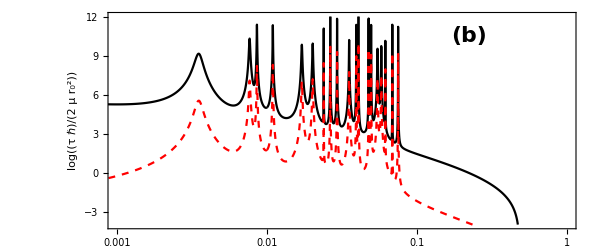

```mathematica
ptdlz=Show[{ptd,plzc},FrameLabel->{{TraditionalForm[Log[(τ ℏ)/(2μ Subscript[r, 0]^2)]  ],TraditionalForm[Style[Log[Subscript[Z, C]],Red]]},{None,None}},PlotRangeClipping->True,Epilog->{Text[Style["(b)",Bold,22],{-1.5,10.5}]}]
```

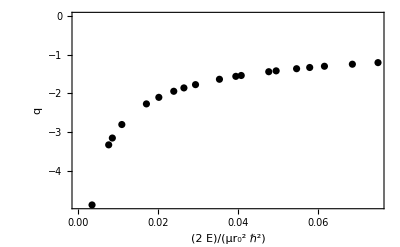

```mathematica
pq=ListPlot[qdata,PlotStyle->Black,Frame->True,LabelStyle->Medium,FrameLabel->{TraditionalForm["E"/(ℏ^2/2 Subscript[μr, 0]^2)],"q"}]
```

```mathematica
xrange
```

{1/1000,1}

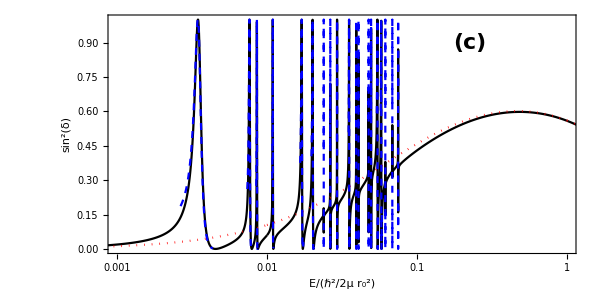

```mathematica
pfanolines = Show[{palsqr,resplots},LabelStyle->Large,PlotRangeClipping->True,Epilog->{Text[Style["(c)",Bold,22],{-1.5,0.9}]}]
```

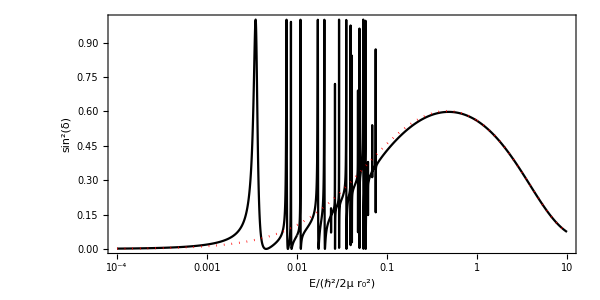

```mathematica
Show[{palsqr},PlotRange->{All,{0,1}}]
```

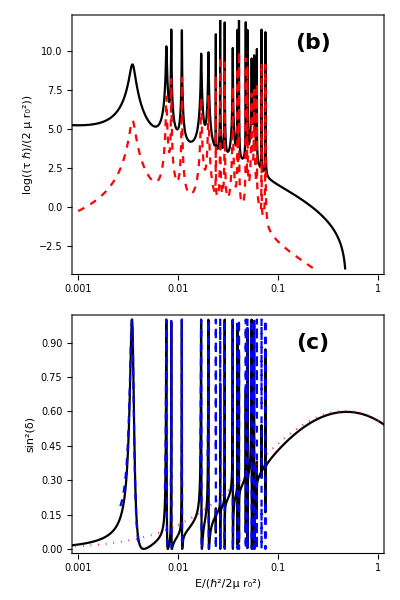

```mathematica
p1=Grid[{{pbsdet},{ptdlz},{pfanolines}},Spacings->0]
```

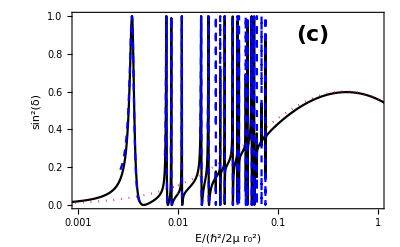

```mathematica
pfanofits=Show[pfanolines,LabelStyle->Medium,ImagePadding->Automatic,ImageSize->Automatic,AspectRatio->1/GoldenRatio,PlotRangeClipping->True]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-fanofits.pdf",pfanofits]
```

~/Code/Nchannel/Square/CODES/plots/p-fanofits.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-poisson-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-poisson-scat.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-wigner-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-wigner-scat.pdf

### Statistical Data

```mathematica
AllWidthData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.800","Table"];
```

```mathematica
AWD=DeleteCases[DeleteCases[AllWidthData,AllWidthData[[1]]],{}];
```

```mathematica
db=0.2;
bins=Table[x,{x,0,3,db}];
bfit=Table[0.5(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}]
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9}

```mathematica
Sdat=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.700","Table"];
SD=DeleteCases[Sdat,Sdat[[1]]];
```

```mathematica
ic=40;
WDtest=Select[AWD,(#1[[3]]==ic)&];
nw=Length[WDtest];
Warray=Table[WDtest[[i,7]],{i,1,nw}];
meanw=Mean[Warray]
wc1=BinCounts[Warray/meanw,{bins}];
wcnorm=Table[{bins[[i]],wc1[[i]]/nw/db},{i,1,Length[bins]-1}];
ν0=0.954;
wcfit=Table[{bfit[[i]],wcnorm[[i,2]]},{i,1,Length[wcnorm]}];
nlm=NonlinearModelFit[wcfit,{γ^(ν/2-1)/Gamma[ν/2] Exp[-γ]},{{ν,1.0}},γ,Method->"LevenbergMarquardt",ConfidenceLevel->0.99];
```

0.00234687

```mathematica
ph=ListPlot[wcnorm,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black];
pe=Plot[γ^(ν/2-1)/Gamma[ν/2] Exp[-γ]/.ν->ν0,{γ,0,5},PlotStyle->{Black,Dashed},PlotRange->All];
```

```mathematica
pb=Plot[γ^(ν/2-1)/Gamma[ν/2] Exp[-γ]/.nlm["BestFitParameters"],{γ,0,3},PlotStyle->{Red},PlotRange->All];
ppt=Plot[Exp[-x/2]/(√(2π x)),{x,0,3},PlotStyle->{Blue,Dashed},Frame->True,PlotRange->All];
```

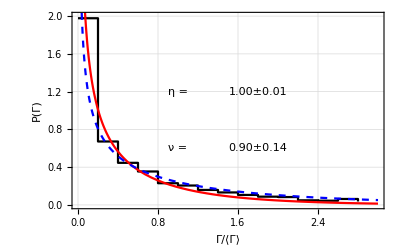

```mathematica
pporterthomas=Show[{ph,pb,ppt},PlotRange->{0,2},Frame->True,GridLines->Automatic,FrameLabel->{"Γ/⟨Γ⟩","P(Γ)"},LabelStyle->Large,Epilog->{Text[Style["η = ",Large],{1.0,1.2}],Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{1.8,1.2}],Text[Style["ν = ",Large],{1.0,0.6}],Text[Style[NumberForm[ν/.nlm["BestFitParameters"],{2,2}]±NumberForm[nlm["ParameterErrors"][[1]],{2,2}],Large],{1.8,0.6}]}]
```

```mathematica
nufitdata=Table[WDtest=Select[AWD,(#1[[3]]==ic)&];
nw=Length[WDtest];
Warray=Table[WDtest[[i,7]],{i,1,nw}];
meanw=Mean[Warray];
wc1=BinCounts[Warray/meanw,{bins}];
wcnorm=Table[{bins[[i]],wc1[[i]]/nw/db},{i,1,Length[bins]-1}];
ν0=0.954;
wcfit=Table[{bfit[[i]],wcnorm[[i,2]]},{i,1,Length[wcnorm]}];
nlm=NonlinearModelFit[wcfit,{γ^(ν/2-1)/Gamma[ν/2] Exp[-γ]},{{ν,1.0}},γ,Method->"LevenbergMarquardt",ConfidenceLevel->0.99];
{{SD[[ic,5]],ν/.nlm["BestFitParameters"]},ErrorBar[nlm["ParameterErrors"][[1]]]},{ic,1,40}]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{{{0.040554,0.919149},ErrorBar[0.132352]},{{0.14387,0.908015},ErrorBar[0.15038]},{{0.24598,0.897885},ErrorBar[0.15833]},{{0.34627,0.911308},ErrorBar[0.135192]},{{0.44425,0.895743},ErrorBar[0.190755]},{{0.5407,0.897836},ErrorBar[0.189901]},{{0.6345,0.909822},ErrorBar[0.14326]},{{0.72648,0.900461},ErrorBar[0.146456]},{{0.81462,0.888232},ErrorBar[0.204745]},{{0.90211,0.891068},ErrorBar[0.185502]},{{0.98872,0.89312},ErrorBar[0.18406]},{{1.0699,0.887901},ErrorBar[0.186749]},{{1.149,0.879677},ErrorBar[0.160175]},{{1.23,0.880911},ErrorBar[0.19053]},{{1.303,0.882435},ErrorBar[0.162255]},{{1.3726,0.886394},ErrorBar[0.209857]},{{1.4425,0.879105},ErrorBar[0.203222]},{{1.5094,0.882044},ErrorBar[0.220368]},{{1.57,0.893809},ErrorBar[0.167948]},{{1.6316,0.896593},ErrorBar[0.165342]},{{1.6942,0.895385},ErrorBar[0.209252]},{{1.7548,0.898207},ErrorBar[0.171951]},{{1.8111,0.900283},ErrorBar[0.16524]},{{1.8607,0.908741},ErrorBar[0.158251]},{{1.9193,0.915544},ErrorBar[0.141009]},{{1.9698,0.910869},ErrorBar[0.135027]},{{2.0213,0.901513},ErrorBar[0.129927]},{{2.0713,0.89695},ErrorBar[0.128037]},{{2.119,0.887674},ErrorBar[0.14044]},{{2.1625,0.893765},ErrorBar[0.200763]},{{2.2031,0.91697},ErrorBar[0.123753]},{{2.2363,0.908925},ErrorBar[0.148784]},{{2.273,0.908821},ErrorBar[0.135194]},{{2.3116,0.905612},ErrorBar[0.185369]},{{2.3438,0.914258},ErrorBar[0.124721]},{{2.3769,0.922841},ErrorBar[0.115029]},{{2.4061,0.917553},ErrorBar[0.163184]},{{2.434,0.919547},ErrorBar[0.119516]},{{2.4671,0.911798},ErrorBar[0.151269]},{{2.4985,0.903742},ErrorBar[0.141151]}}

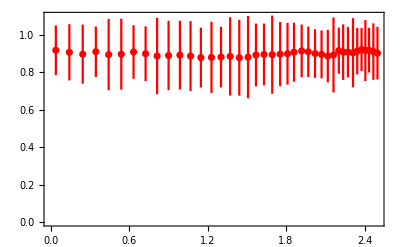

```mathematica
nuplot=ErrorListPlot[nufitdata,Frame->True,LabelStyle->Large,PlotStyle->Red,PlotRange->{0,1.1}]
```

```mathematica
gammazc[ic_]:=Module[{WidthData,i,nw},
WidthData=Select[AWD,(#1[[3]]==ic )&];
nw=Length[WidthData];
Table[{WidthData[[i,7]],WidthData[[i,6]]},{i,1,nw}]
]
```

```mathematica
Allgammazc=Table[{AWD[[i,7]],AWD[[i,6]]},{i,1,Length[AWD]}];
```

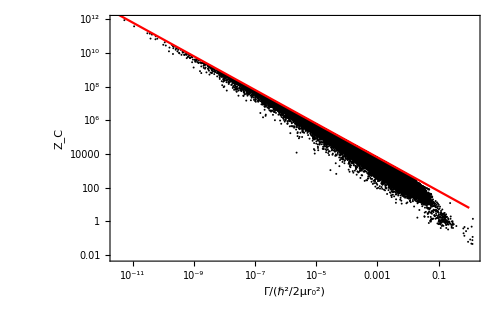

```mathematica
Show[{ListLogLogPlot[Allgammazc,Frame->True,LabelStyle->Large,PlotStyle->Black,FrameLabel->{"Γ/(ℏ^2/2μr_0^2)",TraditionalForm[Subscript[Z, C]]},PlotRange->All],LogLogPlot[A (x)^b/.{A->2π,b->-1},{x,10^-12,1},PlotStyle->Red]},ImageSize->{500,500/1.6}]
```

..

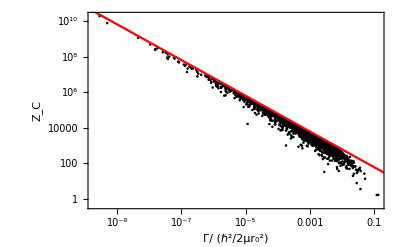

```mathematica
Show[{ListLogLogPlot[gammazc[40],Frame->True,LabelStyle->Large,PlotStyle->Black,FrameLabel->{"Γ/ (ℏ^2/2μr_0^2)",TraditionalForm[Subscript[Z, C]]},PlotRange->All],LogLogPlot[A (x)^b/.{A->2π,b->-1},{x,10^-12,1},PlotStyle->Red]}]
```

```mathematica
Spoles[ic_]:=Module[{WidthData,i,nw},
WidthData=Select[AWD,(#1[[3]]==ic )&];
nw=Length[WidthData];
Table[{WidthData[[i,5]],WidthData[[i,7]]},{i,1,nw}]
]
```

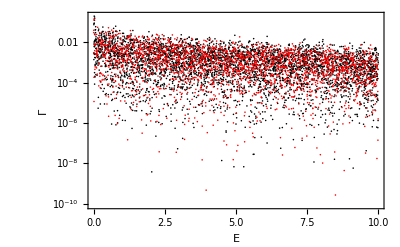

```mathematica
ListLogPlot[{Spoles[1],Spoles[40]},Frame->True,LabelStyle->{Medium},PlotStyle->{Black,Red},FrameLabel->{TraditionalForm["E"],TraditionalForm[Γ]},PlotRange->{{10^-4,10},All}]
```

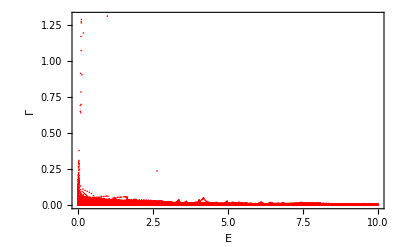

```mathematica
ListPlot[Table[{AWD[[i,5]],AWD[[i,7]]},{i,1,Length[AWD]}],Frame->True,LabelStyle->{Medium},PlotStyle->{Black,Red},FrameLabel->{TraditionalForm["E"],TraditionalForm[Γ]},PlotRange->{{10^-4,10},All}]
```

```mathematica
Sdat=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.700","Table"];
SD=DeleteCases[Sdat,Sdat[[1]]];
```

```mathematica
brodydata=Table[{{SD[[i,5]],SD[[i,7]]},ErrorBar[SD[[i,8]]]},{i,1,Length[SD]}];
gocdata=Table[{SD[[i,5]],SD[[i,4]]},{i,1,Length[SD]}];
```

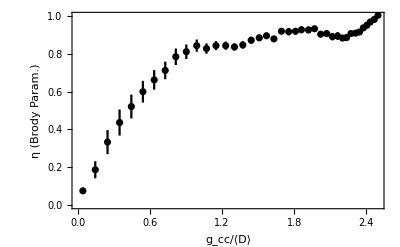

```mathematica
pbrody=ErrorListPlot[{brodydata},Frame->True,PlotStyle->Black,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","η (Brody Param.)"},GridLines->None,PlotRange->{0,1},Epilog->{Inset[ListPlot[gocdata,PlotStyle->Black,Frame->True,FrameLabel->{"g_cc/⟨D⟩","g_oc/⟨D⟩"},LabelStyle->Medium],{1.1,.25},{0,0.25},{3,.6}]}]
```

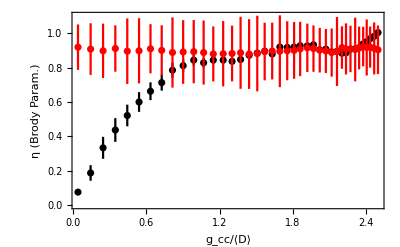

```mathematica
Show[{pbrody,nuplot},PlotRange->{0,1.1}]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pbrody.pdf",pbrody]
```

~/Code/Nchannel/Square/CODES/plots/pbrody.pdf

```mathematica
Posdata=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.500","Table"];
Posdata[[1]]
DeleteCases[Posdata,Posdata[[1]]];
```

{iB,icoup,<D>,goc/<D>,gcc/<D>,<Gamma>/<D>,brody-w,stdev-w,level-spacing-bin-counts.}

```mathematica
dxp=5/20.;
pbins=Table[x,{x,0,5,dxp}];
```

```mathematica
yrange={0,0.85};
impad1={{80,10},{95,5}};
ic=1;
pnorm=Table[{pbins[[i]],Posdata[[ic+1,i+8]]},{i,1,20}];
```

```mathematica
options1={PlotRange->{All,yrange},Frame->True,GridLines->Automatic,FrameLabel->{TraditionalForm[S/⟨D⟩],TraditionalForm[P[S]]},LabelStyle->Large,ImageSize->{450,300},ImagePadding->impad1,FrameTicksStyle->{None,Automatic},AspectRatio->Full};ppoisson=Show[ListPlot[pnorm,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black],Plot[PBrody[SD[[ic,7]],x],{x,0,5},PlotStyle->Red],options1,Epilog->{Text[Style["η = ",Large],{2.5,0.5}],Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{3.9,0.5}]}];
```

```mathematica
ic=40;
impad2={{80,10},{5,5}};
pnorm=Table[{pbins[[i]],Posdata[[ic+1,i+8]]},{i,1,20}];
options={PlotRange->{All,yrange},Frame->True,GridLines->Automatic,FrameLabel->{None,TraditionalForm[P[S]]},LabelStyle->Large,ImageSize->{450,200},ImagePadding->impad2,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},AspectRatio->Full};
pwigner=Show[ListPlot[pnorm,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black],Plot[PBrody[SD[[ic,7]],x],{x,0,5},PlotStyle->Red],options,Epilog->{Text[Style["η = ",Large],{2.5,0.5}],Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{3.9,0.5}]}];
```

```mathematica
ic=8;
pnorm=Table[{pbins[[i]],Posdata[[ic+1,i+8]]},{i,1,20}];
pmiddle=Show[{ListPlot[pnorm,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black],Plot[PBrody[SD[[ic,7]],x],{x,0,5},PlotStyle->Red],Plot[4 s Exp[-2 s],{s,0,5},PlotStyle->{Blue,Dashed}]},options,Epilog->{Text[Style["η = ",Large],{2.5,0.5}],Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{3.9,0.5}]}];
```

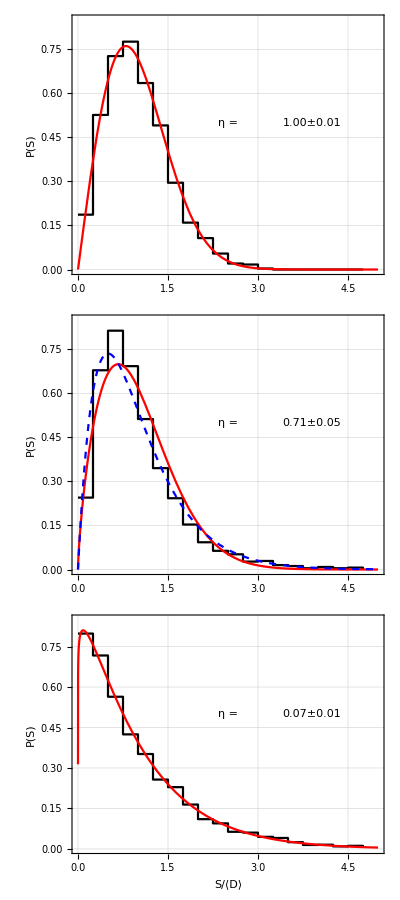

```mathematica
pstats=Grid[{{pwigner},{pmiddle},{ppoisson}},Spacings->0]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pstats.pdf",pstats]
```

~/Code/Nchannel/Square/CODES/plots/pstats.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/ppoisson.pdf",ppoisson]
```

~/Code/Nchannel/Square/CODES/plots/ppoisson.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pwigner.pdf",pwigner]
```

~/Code/Nchannel/Square/CODES/plots/pwigner.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pmiddle.pdf",pmiddle]
```

~/Code/Nchannel/Square/CODES/plots/pmiddle.pdf

### Width data...

```mathematica
avgwidths=Table[{SD[[i,5]],SD[[i,6]]},{i,1,Length[SD]}];
```

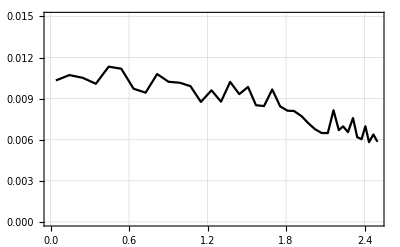

```mathematica
ListPlot[avgwidths,Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic,PlotRange->{0,0.015},Joined->True]
```

```mathematica
ic=30;WindowE=0.2;
MeanW[EE_,WindowE_,ic_]:=Module[{WidthData,i,nw},
WidthData=Select[AWD,(#1[[3]]==ic && EE<#1[[5]]<EE+WindowE)&];
nw=Length[WidthData];
Mean[Table[WidthData[[i,7]],{i,1,nw}]]
]
```

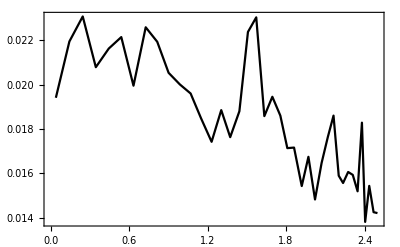

```mathematica
ListPlot[Table[{SD[[ic,5]],MeanW[0.0,10.0,ic]/SD[[ic,3]]},{ic,1,40}],Joined->True,PlotStyle->Black,Frame->True]
```